## 733448815501 - Concatinated successfully

### Observations: Roll further to make it more complete

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Needs["SSSiCv100`"];
733448815501:{"AA"->"AB","BB"->"AA","BA"->"AAB"}
```

```mathematica
rs01=FromReducedRankIndex[733448815501]
```

<|Index→733448815501,QCode→32342434232432334,RuleSet→{AA→AB,BB→AA,BA→AAB}|>

```mathematica
rs01[["RuleSet"]]
```

{AA→AB,BB→AA,BA→AAB}


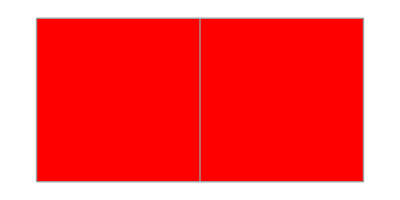


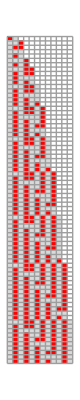
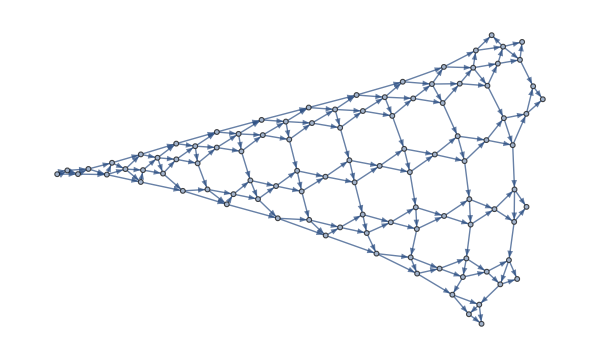
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
sss01=SSS[rs01[["RuleSet"]], "BA",500,
 SSSMax->75,NetMax->100,NetSize->{600,Automatic},SSSSize->{Automatic,380},HighlightMethod->None,RulePlacement->Left,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->True,ImageSize->304.,NetSize->{Automatic,338.},SSSSize->{Automatic,486.},IconSize->{Automatic,31.8},VertexSize->Automatic];
```

```mathematica
sss01[["Net"]]//Short
```

{1→2,1→2,2→3,1→3,2→4,3→4,4→5,«985»,496→498,463→498,498→499,463→499,498→500,499→500}

```mathematica
nds01=ToNetDifferenceSets[sss01[["Net"]]]
```

{{1,1,2},{1,2},{1,2},{1,2},{1,2,4},{1,2},{1,2,3},{3,4},{1,6},{1,3},{1,2,3},{4,5},{1,2},{2,4},{5,6},{1,2,3},{6,7},{1,2},{4,6},{1,2},{1,9},{5,6},{1,2,3},{7,8},{1,2},{5,7},{1,2},{1,2},{6,7},{8,9},{1,2,3},{9,10},{1,2},{7,9},{1,2},{1,2},{8,9},{1,2},{1,12},{8,9},{1,2,3},{10,11},{1,2},{8,10},{1,2},{1,2},{9,10},{1,2},{1,2},{9,10},{11,12},{1,2,3},{12,13},{1,2},{10,12},{1,2},{1,2},{11,12},{1,2},{1,2},{11,12},{1,2},{1,15},{11,12},{1,2,3},{13,14},{1,2},{11,13},{1,2},{1,2},{12,13},{1,2},{1,2},{12,13},{1,2},{1,2},{12,13},{14,15},{1,2,3},{15,16},{1,2},{13,15},{1,2},{1,2},{14,15},{1,2},{1,2},{14,15},{1,2},{1,2},{14,15},{1,2},{1,18},{14,15},{1,2,3},{16,17},{1,2},{14,16},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{17,18},{1,2,3},{18,19},{1,2},{16,18},{1,2},{1,2},{17,18},{1,2},{1,2},{17,18},{1,2},{1,2},{17,18},{1,2},{1,2},{17,18},{1,2},{1,21},{17,18},{1,2,3},{19,20},{1,2},{17,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{20,21},{1,2,3},{21,22},{1,2},{19,21},{1,2},{1,2},{20,21},{1,2},{1,2},{20,21},{1,2},{1,2},{20,21},{1,2},{1,2},{20,21},{1,2},{1,2},{20,21},{1,2},{1,24},{20,21},{1,2,3},{22,23},{1,2},{20,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{23,24},{1,2,3},{24,25},{1,2},{22,24},{1,2},{1,2},{23,24},{1,2},{1,2},{23,24},{1,2},{1,2},{23,24},{1,2},{1,2},{23,24},{1,2},{1,2},{23,24},{1,2},{1,2},{23,24},{1,2},{1,27},{23,24},{1,2,3},{25,26},{1,2},{23,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{26,27},{1,2,3},{27,28},{1,2},{25,27},{1,2},{1,2},{26,27},{1,2},{1,2},{26,27},{1,2},{1,2},{26,27},{1,2},{1,2},{26,27},{1,2},{1,2},{26,27},{1,2},{1,2},{26,27},{1,2},{1,2},{26,27},{1,2},{1,30},{26,27},{1,2,3},{28,29},{1,2},{26,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{29,30},{1,2,3},{30,31},{1,2},{28,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,2},{29,30},{1,2},{1,33},{29,30},{1,2,3},{31,32},{1,2},{29,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{32,33},{1,2,3},{33,34},{1,2},{31,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,2},{32,33},{1,2},{1,36},{32,33},{1,2,3},{34,35},{1,2},{32,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{35,36},{1,2,3},{36,37},{1,2},{34,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{35,36},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1},{},{1,2,3},{},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1}}

```mathematica
rslo1=ReduceSetList[nds01]
```

{{1,1,2},€^3[{1,2}],{1,2,4},{1,2},{1,2,3},{3,4},€_(n$1⊨1)^2[{1,6-3 (-1+n$1)}],{1,2,3},{4,5},{1,2},€_(n$1⊨1)^2[{2+3 (-1+n$1),4+2 (-1+n$1)}],{1,2,3},{6,7},{1,2},{4,6},€_(n$3⊨1)^2[€_(n$1⊨1)^2[{1,7-5 n$1+12 (-1+n$1) n$3}],€_(n$2⊨1)^2[{-10+3 n$2+12 n$3,3 (-3+n$2+4 n$3)},{1,2,3},{-7+2 n$2+12 n$3,2 (-3+n$2+6 n$3)},{1,2},{-9+2 n$2+12 n$3,-7+2 n$2+12 n$3},€^(-3+4 n$3)[€^2[{1,2}],{2 (-4+n$2+6 n$3),-7+2 n$2+12 n$3}]],€_(n$1⊨1)^2[{1,4-2 n$1+12 (-1+n$1) n$3}],€_(n$2⊨1)^2[{-7+3 n$2+12 n$3,3 (-2+n$2+4 n$3)},{1,2,3},{2 (-2+n$2+6 n$3),-3+2 n$2+12 n$3},{1,2},{2 (-3+n$2+6 n$3),2 (-2+n$2+6 n$3)},€^(-2+4 n$3)[€^2[{1,2}],{-5+2 n$2+12 n$3,2 (-2+n$2+6 n$3)}]],€_(n$1⊨1)^2[{1,1+n$1+12 (-1+n$1) n$3}],€_(n$2⊨1)^2[{-4+3 n$2+12 n$3,3 (-1+n$2+4 n$3)},{1,2,3},{-1+2 n$2+12 n$3,2 (n$2+6 n$3)},{1,2},{-3+2 n$2+12 n$3,-1+2 n$2+12 n$3},€^(-1+4 n$3)[€^2[{1,2}],{2 (-1+n$2+6 n$3),-1+2 n$2+12 n$3}]],€_(n$1⊨1)^2[{1,-2+4 n$1+12 (-1+n$1) n$3}],€_(n$2⊨1)^2[{-1+3 n$2+12 n$3,3 (n$2+4 n$3)},{1,2,3},{2 (1+n$2+6 n$3),3+2 n$2+12 n$3},{1,2},{2 (n$2+6 n$3),2 (1+n$2+6 n$3)},€^(4 n$3)[€^2[{1,2}],{1+2 n$2+12 n$3,2 (1+n$2+6 n$3)}]]],€_(n$1⊨1)^2[{1,-5+24 (-1+n$1)+7 n$1}],€_(n$2⊨1)^2[{29+3 (-1+n$2),30+3 (-1+n$2)},{1,2,3},{31+2 (-1+n$2),32+2 (-1+n$2)},{1,2},{29+2 (-1+n$2),31+2 (-1+n$2)},€^9[€^2[{1,2}],{30+2 (-1+n$2),31+2 (-1+n$2)}]],€_(n$1⊨1)^2[{1,2+34 (-1+n$1)}],€_(n$2⊨1)^2[{32+3 (-1+n$2),33+3 (-1+n$2)},{1,2,3},{34+2 (-1+n$2),35+2 (-1+n$2)},{1,2},{32+2 (-1+n$2),34+2 (-1+n$2)},€^(10-2 (-1+n$2))[€^2[{1,2}],{33+2 (-1+n$2),34+2 (-1+n$2)}]],€^2[€^2[{1,2}],{}],{1,2},{1},{},{1,2,3},{},{1,2},€^7[{},€^2[{1,2}]],{},{1,2},{1}}